```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};
Wxmin= {2,3,1};
Wxmax= {5,3,1};
Hymin= {3,2,1};
Hymax= {3,5,1};
WorldPoints = {a,b,c,d,aPrime,bPrime,cPrime,dPrime,d2Prime};
Oc={0,0,0,1};
zeta1 = -1;
zeta2=-1;
alpha=45;
beta = 0;
Oc2={6,0,0,1};
Rot2=RotationsE2[alpha];
Rot1=RotationsE2[beta];
ObjectSize = b[[1]]-a[[1]];
A={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
AK={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
ClearAll["Global`*"];
```

PM1 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

OC2 = {6,0,0,1}

M of C2=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

M2 of C1 =(0.707107 | 0. | -0.707107 | -4.24264
0. | 1. | 0. | 0.
0.707107 | 0. | 0.707107 | -4.24264
0. | 0. | 0. | 1.)

ProjectionMtxCamera1(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 1 | 0)

ProjectionMtxCamera2(-0.707107 | 0. | 0.707107 | 4.24264
0. | -1. | 0. | 0.
-0.707107 | 0. | -0.707107 | 4.24264
0.707107 | 0. | 0.707107 | -4.24264)

CameraProjectedPointsK1 = (-3 | -3 | 4 | -4
-5 | -3 | 4 | -4
-5 | -5 | 4 | -4
-3 | -5 | 4 | -4
-3 | -3 | 6 | -6
-5 | -3 | 6 | -6
-5 | -5 | 6 | -6
-3 | -5 | 6 | -6
-8 | -8 | 6 | -6)

CameraProjectedPointsK2 = (-0.707107 | -3. | 4.94975 | -4.94975
-2.12132 | -3. | 3.53553 | -3.53553
-2.12132 | -5. | 3.53553 | -3.53553
-0.707107 | -5. | 4.94975 | -4.94975
-2.12132 | -3. | 6.36396 | -6.36396
-3.53553 | -3. | 4.94975 | -4.94975
-3.53553 | -5. | 4.94975 | -4.94975
-2.12132 | -5. | 6.36396 | -6.36396
-5.65685 | -8. | 2.82843 | -2.82843)

homogene CameraProjectedPointsK1 = (3/4 | 3/4 | -1 | 1
5/4 | 3/4 | -1 | 1
5/4 | 5/4 | -1 | 1
3/4 | 5/4 | -1 | 1
1/2 | 1/2 | -1 | 1
5/6 | 1/2 | -1 | 1
5/6 | 5/6 | -1 | 1
1/2 | 5/6 | -1 | 1
4/3 | 4/3 | -1 | 1)

homogene CameraProjectedPointsK2 = (0.142857 | 0.606092 | -1. | 1.
0.6 | 0.848528 | -1. | 1.
0.6 | 1.41421 | -1. | 1.
0.142857 | 1.01015 | -1. | 1.
0.333333 | 0.471405 | -1. | 1.
0.714286 | 0.606092 | -1. | 1.
0.714286 | 1.01015 | -1. | 1.
0.333333 | 0.785674 | -1. | 1.
2. | 2.82843 | -1. | 1.)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

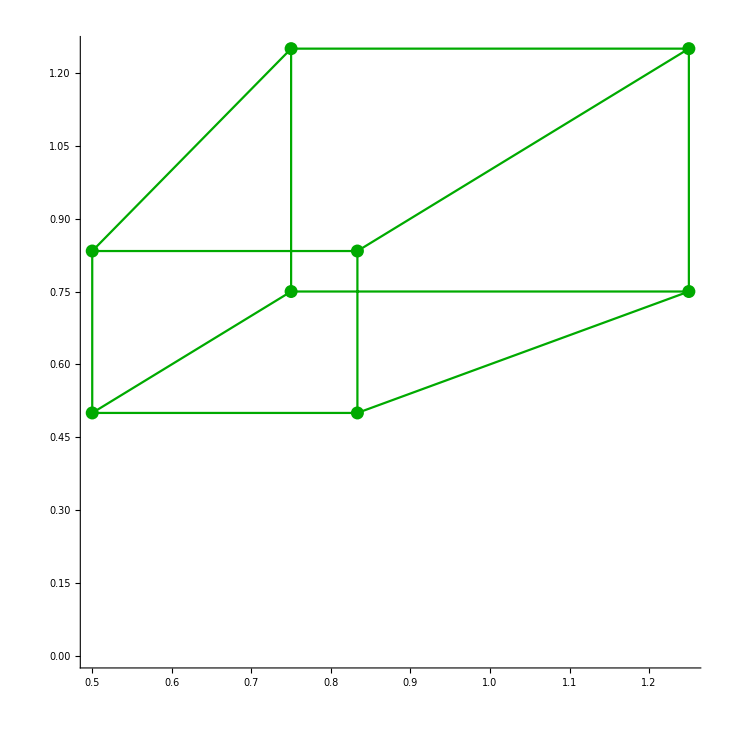

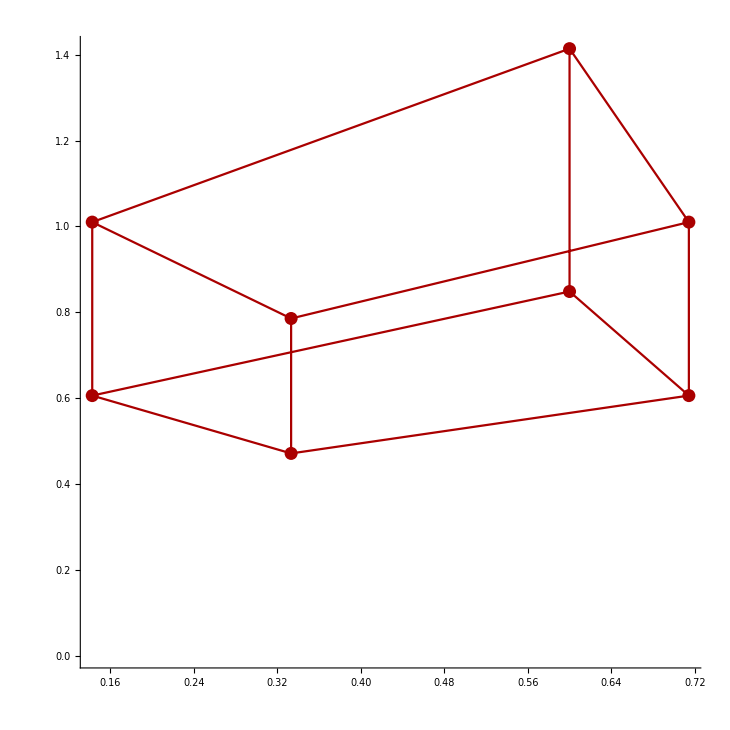

ImagePlaneC1Points = (3/4 | 3/4 | 1
5/4 | 3/4 | 1
5/4 | 5/4 | 1
3/4 | 5/4 | 1
1/2 | 1/2 | 1
5/6 | 1/2 | 1
5/6 | 5/6 | 1
1/2 | 5/6 | 1
4/3 | 4/3 | 1)

ImagePlaneC2Points = (0.142857 | 0.606092 | 1.
0.6 | 0.848528 | 1.
0.6 | 1.41421 | 1.
0.142857 | 1.01015 | 1.
0.333333 | 0.471405 | 1.
0.714286 | 0.606092 | 1.
0.714286 | 1.01015 | 1.
0.333333 | 0.785674 | 1.
2. | 2.82843 | 1.)

CoefficientMtx = (0.107143 | 0.107143 | 0.142857 | 0.454569 | 0.454569 | 0.606092 | 0.75 | 0.75 | 1.
0.75 | 0.45 | 0.6 | 1.06066 | 0.636396 | 0.848528 | 1.25 | 0.75 | 1.
0.75 | 0.75 | 0.6 | 1.76777 | 1.76777 | 1.41421 | 1.25 | 1.25 | 1.
0.107143 | 0.178571 | 0.142857 | 0.757614 | 1.26269 | 1.01015 | 0.75 | 1.25 | 1.
0.166667 | 0.166667 | 0.333333 | 0.235702 | 0.235702 | 0.471405 | 0.5 | 0.5 | 1.
0.595238 | 0.357143 | 0.714286 | 0.505076 | 0.303046 | 0.606092 | 0.833333 | 0.5 | 1.
0.595238 | 0.595238 | 0.714286 | 0.841794 | 0.841794 | 1.01015 | 0.833333 | 0.833333 | 1.
0.166667 | 0.277778 | 0.333333 | 0.392837 | 0.654729 | 0.785674 | 0.5 | 0.833333 | 1.
2.66667 | 2.66667 | 2. | 3.77124 | 3.77124 | 2.82843 | 1.33333 | 1.33333 | 1.)

MatrixRank[CoefficientMtx]8

ns ={{-1.15097×10^-15,-0.5,-4.83539×10^-16,-2.15×10^-15,1.24806×10^-15,0.707107,2.20854×10^-15,-0.5,-2.18226×10^-16}}

F = (-1.15097×10^-15 | -0.5 | -4.83539×10^-16
-2.15×10^-15 | 1.24806×10^-15 | 0.707107
2.20854×10^-15 | -0.5 | -2.18226×10^-16)

lC1 = {{-0.375,0.707107,-0.375},{-0.375,0.707107,-0.375},{-0.625,0.707107,-0.625},{-0.625,0.707107,-0.625},{-0.25,0.707107,-0.25},{-0.25,0.707107,-0.25},{-0.416667,0.707107,-0.416667},{-0.416667,0.707107,-0.416667},{-0.666667,0.707107,-0.666667}}

lPrimeC1 = {{7.41017×10^-16,-0.571429,0.428571},{-3.06379×10^-16,-0.8,0.6},{-1.5226×10^-15,-0.8,1.},{-1.27713×10^-16,-0.571429,0.714286},{8.11361×10^-16,-0.666667,0.333333},{8.33194×10^-17,-0.857143,0.428571},{-7.85411×10^-16,-0.857143,0.714286},{1.35682×10^-16,-0.666667,0.555556},{-6.17452×10^-15,-1.5,2.}}

e = {1.,1.22125×10^-15,3.04382×10^-15}

e' = {0.707107,4.47613×10^-16,-0.707107}

EpipoleLines = (1. | -1.88562 | 1.
1. | -1.88562 | 1.
1. | -1.13137 | 1.
1. | -1.13137 | 1.
1. | -2.82843 | 1.
1. | -2.82843 | 1.
1. | -1.69706 | 1.
1. | -1.69706 | 1.
1. | -1.06066 | 1.)

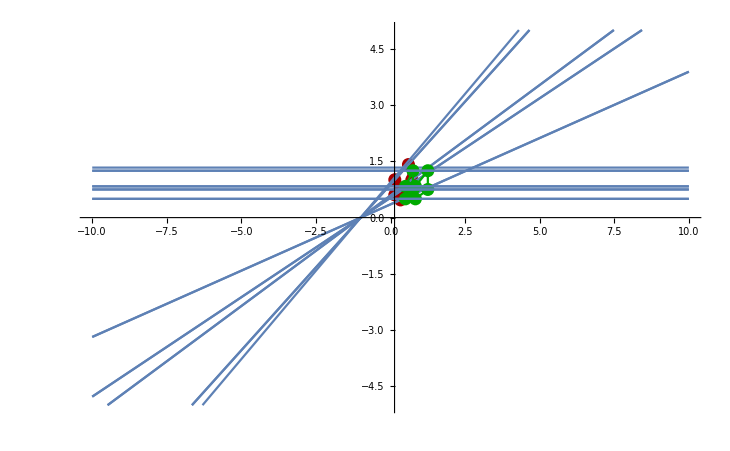

Begin Computing essential Matrix___________________________________________________

EMtx = (-1.15097×10^-15 | -0.5 | 4.83539×10^-16
-2.15×10^-15 | 1.24806×10^-15 | -0.707107
-2.20854×10^-15 | 0.5 | -2.18226×10^-16)

U of E = {{0.,0.707107,-0.707107},{-1.,-2.26667×10^-16,-2.26667×10^-16},{3.33067×10^-16,-0.707107,-0.707107}}

Sigma of E = {{0.707107,0.,0.},{0.,0.707107,0.},{0.,0.,0.}}

V of E = {{3.14047×10^-15,9.99201×10^-16,1.},{9.67078×10^-16,-1.,1.22125×10^-15},{1.,9.67078×10^-16,-3.04382×10^-15}}

S1 = (0. | -0.707107 | 2.35514×10^-16
0.707107 | 0. | -0.707107
-2.35514×10^-16 | 0.707107 | 0.)

S2 = (0. | 0.707107 | -2.35514×10^-16
-0.707107 | 0. | 0.707107
2.35514×10^-16 | -0.707107 | 0.)

R1 = (0.707107 | 1.54738×10^-15 | 0.707107
1.22587×10^-15 | -1. | 7.40412×10^-16
0.707107 | 5.1279×10^-16 | -0.707107)

R2 = (0.707107 | 1.79723×10^-16 | -0.707107
-7.72534×10^-16 | 1. | -7.40412×10^-16
0.707107 | 1.21431×10^-15 | 0.707107)

Test R1 is rotation ={{1.,2.30892×10^-16,1.11022×10^-16},{2.30892×10^-16,1.,-8.84734×10^-18},{1.11022×10^-16,-8.84734×10^-18,1.}}

Test R2 is rotation ={{1.,2.13197×10^-16,1.11022×10^-16},{2.13197×10^-16,1.,-8.84734×10^-18},{1.11022×10^-16,-8.84734×10^-18,1.}}

Check if t of S1, S2 is equal = {{{0.707107,2.22045×10^-16,0.707107}},{{0.707107,2.22045×10^-16,0.707107}}}

t = {0.707107,2.22045×10^-16,0.707107}

P21  = (0.707107 | 1.79723×10^-16 | -0.707107 | -0.707107
-7.72534×10^-16 | 1. | -7.40412×10^-16 | -2.22045×10^-16
0.707107 | 1.21431×10^-15 | 0.707107 | -0.707107)

P22  = (0.707107 | 1.54738×10^-15 | 0.707107 | -0.707107
1.22587×10^-15 | -1. | 7.40412×10^-16 | -2.22045×10^-16
0.707107 | 5.1279×10^-16 | -0.707107 | -0.707107)

P23  = (0.707107 | 1.79723×10^-16 | -0.707107 | 0.707107
-7.72534×10^-16 | 1. | -7.40412×10^-16 | 2.22045×10^-16
0.707107 | 1.21431×10^-15 | 0.707107 | 0.707107)

P24  = (0.707107 | 1.54738×10^-15 | 0.707107 | 0.707107
1.22587×10^-15 | -1. | 7.40412×10^-16 | 2.22045×10^-16
0.707107 | 5.1279×10^-16 | -0.707107 | 0.707107)

End Computing essential Matrix___________________________________________________

PList = {{{0.707107,1.79723×10^-16,-0.707107,-0.707107},{-7.72534×10^-16,1.,-7.40412×10^-16,-2.22045×10^-16},{0.707107,1.21431×10^-15,0.707107,-0.707107}},{{0.707107,1.54738×10^-15,0.707107,-0.707107},{1.22587×10^-15,-1.,7.40412×10^-16,-2.22045×10^-16},{0.707107,5.1279×10^-16,-0.707107,-0.707107}},{{0.707107,1.79723×10^-16,-0.707107,0.707107},{-7.72534×10^-16,1.,-7.40412×10^-16,2.22045×10^-16},{0.707107,1.21431×10^-15,0.707107,0.707107}},{{0.707107,1.54738×10^-15,0.707107,0.707107},{1.22587×10^-15,-1.,7.40412×10^-16,2.22045×10^-16},{0.707107,5.1279×10^-16,-0.707107,0.707107}}}

Length PList = 4

End Reconstruction of Rotation and Translation________________________________________________

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{0.5,0.5,-0.666667},{0.833333,0.5,-0.666667},{0.833333,0.833333,-0.666667},{0.5,0.833333,-0.666667},{0.5,0.5,-1.},{0.833333,0.5,-1.},{0.833333,0.833333,-1.},{0.5,0.833333,-1.},{1.33333,1.33333,-1.}}

ScaleValue = 6.

RForOk2 = {{0.707107,-7.72534×10^-16,0.707107},{1.79723×10^-16,1.,1.21431×10^-15},{-0.707107,-7.40412×10^-16,0.707107}}

tForOK2 = {-0.707107,-2.22045×10^-16,-0.707107}

t = {1.,1.20778×10^-15,-2.94209×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
5. | 3. | -4.
5. | 5. | -4.
3. | 5. | -4.
3. | 3. | -6.
5. | 3. | -6.
5. | 5. | -6.
3. | 5. | -6.
8. | 8. | -6.)

-Graphics3D-

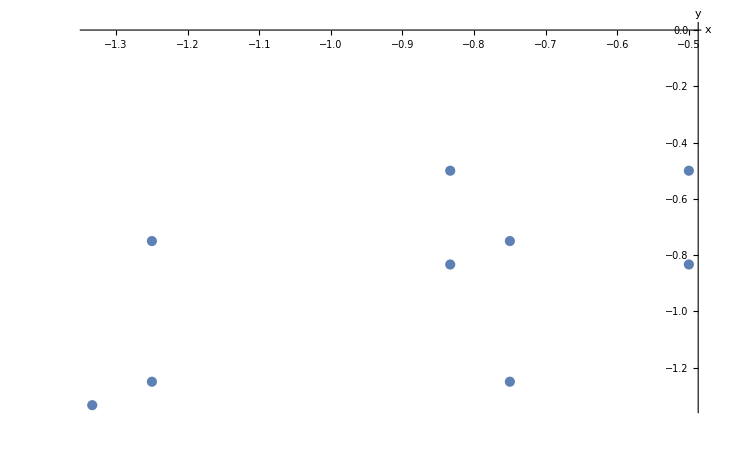

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{6.82286×10^13,6.82286×10^13,-9.09715×10^13},{1.25,0.75,-1.},{1.25,1.25,-1.},{7.65344×10^13,1.27557×10^14,-1.02046×10^14},{5.88356×10^13,5.88356×10^13,-1.17671×10^14},{1.25,0.75,-1.5},{1.25,1.25,-1.5},{5.91809×10^13,9.86348×10^13,-1.18362×10^14},{0.8,0.8,-0.6}}

ScaleValue = 4.39698×10^-14

RForOk2 = {{0.707107,1.22587×10^-15,0.707107},{1.54738×10^-15,-1.,5.1279×10^-16},{0.707107,7.40412×10^-16,-0.707107}}

tForOK2 = {-0.707107,-2.22045×10^-16,-0.707107}

t = {1.,1.23471×10^-15,-2.9976×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
5.49623×10^-14 | 3.29774×10^-14 | -4.39698×10^-14
5.49623×10^-14 | 5.49623×10^-14 | -4.39698×10^-14
3.3652 | 5.60867 | -4.48694
2.58699 | 2.58699 | -5.17398
5.49623×10^-14 | 3.29774×10^-14 | -6.59548×10^-14
5.49623×10^-14 | 5.49623×10^-14 | -6.59548×10^-14
2.60217 | 4.33696 | -5.20435
3.51759×10^-14 | 3.51759×10^-14 | -2.63819×10^-14)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-0.5,-0.5,0.666667},{-0.833333,-0.5,0.666667},{-0.833333,-0.833333,0.666667},{-0.5,-0.833333,0.666667},{-0.5,-0.5,1.},{-0.833333,-0.5,1.},{-0.833333,-0.833333,1.},{-0.5,-0.833333,1.},{-1.33333,-1.33333,1.}}

ScaleValue = -6.

RForOk2 = {{0.707107,-7.72534×10^-16,0.707107},{1.79723×10^-16,1.,1.21431×10^-15},{-0.707107,-7.40412×10^-16,0.707107}}

tForOK2 = {0.707107,2.22045×10^-16,0.707107}

t = {-1.,-1.20778×10^-15,2.94209×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
5. | 3. | -4.
5. | 5. | -4.
3. | 5. | -4.
3. | 3. | -6.
5. | 3. | -6.
5. | 5. | -6.
3. | 5. | -6.
8. | 8. | -6.)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-6.82286×10^13,-6.82286×10^13,9.09715×10^13},{-1.25,-0.75,1.},{-1.25,-1.25,1.},{-7.65344×10^13,-1.27557×10^14,1.02046×10^14},{-5.88356×10^13,-5.88356×10^13,1.17671×10^14},{-1.25,-0.75,1.5},{-1.25,-1.25,1.5},{-5.91809×10^13,-9.86348×10^13,1.18362×10^14},{-0.8,-0.8,0.6}}

ScaleValue = -4.39698×10^-14

RForOk2 = {{0.707107,1.22587×10^-15,0.707107},{1.54738×10^-15,-1.,5.1279×10^-16},{0.707107,7.40412×10^-16,-0.707107}}

tForOK2 = {0.707107,2.22045×10^-16,0.707107}

t = {-1.,-1.23471×10^-15,2.9976×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
5.49623×10^-14 | 3.29774×10^-14 | -4.39698×10^-14
5.49623×10^-14 | 5.49623×10^-14 | -4.39698×10^-14
3.3652 | 5.60867 | -4.48694
2.58699 | 2.58699 | -5.17398
5.49623×10^-14 | 3.29774×10^-14 | -6.59548×10^-14
5.49623×10^-14 | 5.49623×10^-14 | -6.59548×10^-14
2.60217 | 4.33696 | -5.20435
3.51759×10^-14 | 3.51759×10^-14 | -2.63819×10^-14)

-Graphics3D-

-Graphics-

Begin New Rectification with Disortion minimization criterion_______________________________________________

pi = {{0.75,0.75,1.},{1.25,0.75,1.},{1.25,1.25,1.},{0.75,1.25,1.},{0.5,0.5,1.},{0.833333,0.5,1.},{0.833333,0.833333,1.},{0.5,0.833333,1.},{1.33333,1.33333,1.}}

pj = {{0.142857,0.606092,1.},{0.6,0.848528,1.},{0.6,1.41421,1.},{0.142857,1.01015,1.},{0.333333,0.471405,1.},{0.714286,0.606092,1.},{0.714286,1.01015,1.},{0.333333,0.785674,1.},{2.,2.82843,1.}}

n = 9

minXpi = 0.5

maxXPi = 1.33333

minYpi = 0.5

maxYPi = 1.33333

minXPj = 0.142857

maxXPj = 2.

minYPj = 0.471405

maxYPj = 2.82843

piWidth = 3.

piHeight = 3.

pjWidth = 3.

pjHeight = 3.

pc = (0.888889
0.888889
1.)

pcPrime = (0.620106
1.06453
1.)

P = {{-0.138889,0.361111,0.361111,-0.138889,-0.388889,-0.0555556,-0.0555556,-0.388889,0.444444},{-0.138889,-0.138889,0.361111,0.361111,-0.388889,-0.388889,-0.0555556,-0.0555556,0.444444},{0.,0.,0.,0.,0.,0.,0.,0.,0.}}

PPrime = {{-0.477249,-0.0201058,-0.0201058,-0.477249,-0.286772,0.0941799,0.0941799,-0.286772,1.37989},{-0.458435,-0.215998,0.349687,-0.0543736,-0.593122,-0.458435,-0.0543736,-0.278852,1.7639},{0.,0.,0.,0.,0.,0.,0.,0.,0.}}

PP = {{0.805556,0.444444,0.},{0.444444,0.805556,0.},{0.,0.,0.}}

PPPrime = {{2.54267,2.87781,0.},{2.87781,4.13607,0.},{0.,0.,0.}}

pc = {0.888889,0.888889,1.}

pcpc = {{0.790123,0.790123,0.888889},{0.790123,0.790123,0.888889},{0.888889,0.888889,1.}}

pcpcPrime = {{0.384531,0.660119,0.620106},{0.660119,1.13322,1.06453},{0.620106,1.06453,1.}}

A = (7.46336×10^-30 | -4.11772×10^-30 | -2.45197×10^-15
-4.11772×10^-30 | 7.46336×10^-30 | 1.35281×10^-15
-2.45197×10^-15 | 1.35281×10^-15 | 0.805556)

B = (5.26579×10^-31 | 6.85343×10^-16 | -4.56104×10^-16
6.85343×10^-16 | 0.891975 | -0.593621
-4.56104×10^-16 | -0.593621 | 0.395062)

APrime = (2.06804 | -1.4389 | 2.06804
-1.4389 | 1.27133 | -1.4389
2.06804 | -1.4389 | 2.06804)

BPrime = (5.66637×10^-31 | 1.07998×10^-15 | 1.03089×10^-15
4.22572×10^-16 | -1.07623×10^-15 | -0.400652
3.83889×10^-31 | -0.572794 | -1.64266×10^-16)

{A[[1,1;;2]],A[[2,1;;2]]}={{7.46336×10^-30,-4.11772×10^-30},{-4.11772×10^-30,7.46336×10^-30}}

{APrime[[1,1;;2]],APrime[[2,1;;2]]}={{2.06804,-1.4389},{-1.4389,1.27133}}

DD ={{2.73192×10^-15,-1.50726×10^-15},{0.,2.27849×10^-15}}

DDPrime ={{1.43807,-1.00058},{0.,0.519777}}

{B[[1,1;;2]],B[[2,1;;2]]}={{5.26579×10^-31,6.85343×10^-16},{6.85343×10^-16,0.891975}}

{BPrime[[1,1;;2]],BPrime[[2,1;;2]]}={{5.66637×10^-31,1.07998×10^-15},{4.22572×10^-16,-1.07623×10^-15}}

DTBD[[2,1]] = {6.40819×10^-16,1.}

Eigensystem DTB1 = {{1.71814×10^29,1.249×10^-16},{{6.40819×10^-16,1.},{-1.,6.40819×10^-16}}}

Eigensystem DTBPrimeD = {{-9.62531×10^-16,8.48615×10^-16},{{-0.832236,0.554422},{0.862271,0.506447}}}

z1 first = {2.42145×10^14,4.38887×10^14}

z1= {2.42145×10^14,4.38887×10^14}

z2 first = {0.16344,1.06665}

z2 second = {1.27754,0.974353}

z2= {1.27754,0.974353}

z ={5.01254×10^14,5.01254×10^14,0.}

w = {-1.52573,1.52573,5.01254×10^14}

wPrime = {-2.50627×10^14,-0.452101,-2.50627×10^14}

wPrime = {1.,1.80388×10^-15,1.}

w = {-3.04382×10^-15,3.04382×10^-15,1.}

HpPrime = (1. | 0. | 0.
0. | 1. | 0.
1. | 1.80388×10^-15 | 1.)

Hp = (1. | 0. | 0.
0. | 1. | 0.
-3.04382×10^-15 | 3.04382×10^-15 | 1.)

ePrime inf = {0.707107,4.47613×10^-16,6.32827×10^-15}

e inf = {1.,1.22125×10^-15,-3.9443×10^-31}

HrPrime = (-0.707107 | -2.65313×10^-16 | 0.
2.65313×10^-16 | -0.707107 | 0.705
0. | 0. | 1.)

Hr = (-0.5 | -2.20854×10^-15 | 0.
2.20854×10^-15 | -0.5 | 0.705
0. | 0. | 1.)

ePrimeHorizontal = {-0.5,4.33253×10^-15,6.32827×10^-15}

eHorizontal = {-0.5,1.59791×10^-15,-3.9443×10^-31}

piA = {-0.75,0.705,1.}

piB = {-1.5,-0.045,1.}

piC = {-0.75,-0.795,1.}

piD = {-3.31281×10^-15,-0.045,1.}

piX = {-1.5,2.22045×10^-16,-9.10383×10^-15}

piY = {-6.66134×10^-15,-1.5,9.10383×10^-15}

piSA = -1.

piSB = 4.29286×10^-15

pjA = {-1.06066,1.7625,2.5}

pjB = {-2.12132,1.75934,4.}

pjC = {-1.06066,-0.35882,2.5}

pjD = {-3.9797×10^-16,-0.35566,1.}

pjX = {-2.12132,2.115,3.}

pjY = {-8.88178×10^-16,-2.12132,5.32907×10^-15}

pjSA = -1.99405

pjSB = -0.997021

RecPointsC1 =(0.75 | 0.75 | 1.
1.25 | 0.75 | 1.
1.25 | 1.25 | 1.
0.75 | 1.25 | 1.
0.5 | 0.5 | 1.
0.833333 | 0.5 | 1.
0.833333 | 0.833333 | 1.
0.5 | 0.833333 | 1.)

RecPointsC2 =(0.125 | 0.53033 | 1.
0.375 | 0.53033 | 1.
0.375 | 0.883883 | 1.
0.125 | 0.883883 | 1.
0.25 | 0.353553 | 1.
0.416667 | 0.353553 | 1.
0.416667 | 0.589256 | 1.
0.25 | 0.589256 | 1.)

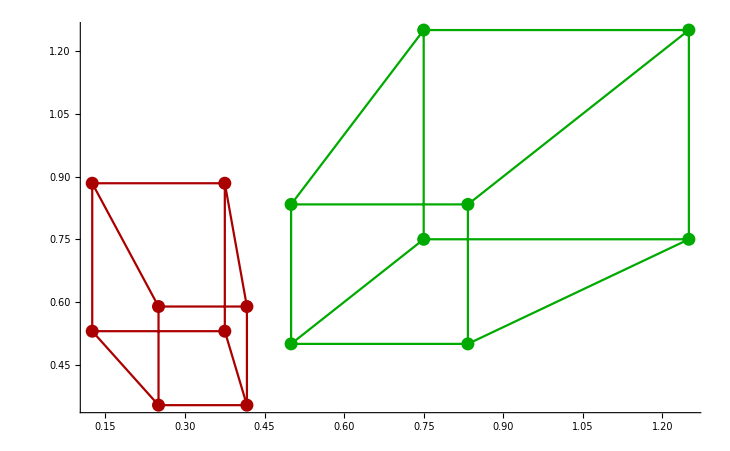

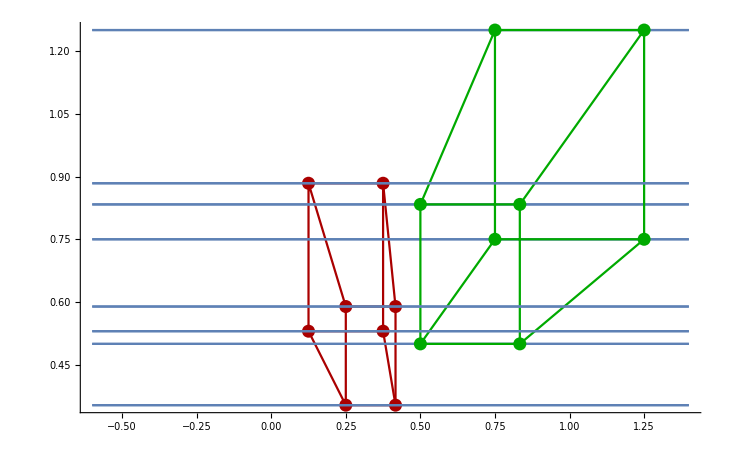

End New Rectification with Disortion minimization criterion_______________________________________________

```mathematica
StartComputation[];
```